### The effective Hamiltonian of the Rabi model

Data are imported from julia code https : // github . com/djuliannader/RabiModel

```mathematica
R=50; (*quibit frequency*)
H[q_,p_]=(q^2+p^2)/2-(1/2)*(1+(Sqrt[2]*g*q+λ)^2)^(1/2);
V[q_,gg_,λλ_]=q^2/2-(1/2)*(1+(Sqrt[2]*gg*q+λλ)^2)^(1/2);
```

#### Normal phase

```mathematica
g=1/2^(1/2); (*coupling*)
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst]}],{en,-0.499,-0.2,0.0001}];
```

```mathematica
datarho={{-24.42505838235548, 0.6971599105424998},
{-22.978597968671373, 0.6856219724536073},
{-21.50974392668985, 0.6760509761245694},
{-20.021565847933044, 0.6679233603447005},
{-18.51642851652634, 0.6608962041051417},
{-16.996210178274655, 0.6547331626589479},
{-15.46243845092786 ,0.6492647770258408},
{-13.916379652385103, 0.6443656378827293},
{-12.359100048449115, 0.6399404937140422},
{-10.791509304760435, 0.6359154105801086},
{-9.214392194596421, 0.6322319329555061},
{-7.628432291832355, 0.6288431038648016},
{-6.034230037120754, 0.6257106785230641},
{-4.432316756932385 ,0.6228031277491014},
{-2.8231657098653926, 0.6200941779560755},
{-1.2072009088810005, 0.617561724224336}};
dataT=Table[{datarho[[i,1]]/R,4π*datarho[[i,2]]},{i,1,12}];
```

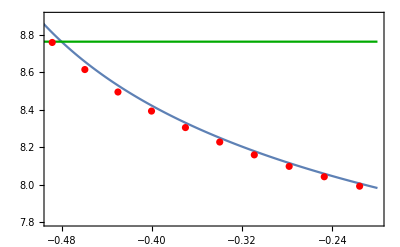

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.49,-0.2},{8.9,7.8}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black}],ListPlot[{dataT},PlotStyle->Red],Plot[8.765,{x,-0.5,-0.2},PlotStyle->{Darker[Green]}],Axes->False]
```

#### Superradiant phase

```mathematica
g=2^(1/2);
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,4}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
qtp3=qtpsort[[3]];
qtp4=qtpsort[[4]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
rhoinst2=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp3,qtp4}];
AppendTo[rho1,{en,Re[rhoinst1]+Re[rhoinst2]}],{en,-0.625,-0.5005,0.001}];
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst1]}],{en,-0.4995,-0.2,0.001}];
```

```mathematica
datarho={{-30.891219305606537, 1.1695581680077685},
{-30.04260636181629, 1.1873633947991613},
{-29.208146602107433, 1.2096032247387658},
{-28.391090381025087, 1.2385510363574008},
{-27.59651813942441, 1.2791822832122397},
{-26.83507863412209, 1.3492916815959293},
{-26.139603353463514, 1.538885407927282},
{-25.54456999623379, 1.8510094712153373},
{-24.95239642737438, 1.552550606222522},
{-24.24517513209946, 1.2981260723802746},
{-23.44078284759713, 1.192686399967416},
{-22.578109960689982, 1.127519771516704},
{-21.67119809397417, 1.0788402123847443},
{-20.726930330269944, 1.0399180860026467},
{-19.74992925719839, 1.0076704432958266},
{-18.743692741111108, 0.9803103801102522},
{-17.711012369128973, 0.9566854388511927},
{-16.65418874361456, 0.9360039193903286},
{-15.57516091553309, 0.9176971889017521},
{-14.475590926826523, 0.9013427082840794},
{-13.356921990084446, 0.8866176050747027},
{-12.220418561687309, 0.8732671874047547},
{-11.067183965099606, 0.861071092556607},
{-9.898107357235038 ,0.8497556242712736},
{-8.713536923041564 ,0.8386926164900954},
{-7.512133158602792 ,0.8261215795035435},
{-6.288283790596326, 0.8082616276609726},
{-5.029196292886644, 0.7806694736220358},
{-3.7156384812107106, 0.7428516601282767},
{-2.3279186876507234, 0.6996550254120536},
{-0.8516994442146141, 0.6565286900820524}};
dataT=Table[{datarho[[i,1]]/R,4π*datarho[[i,2]]},{i,1,Length[datarho]}];
```

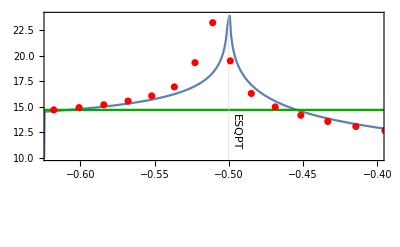

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{-.5},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.62,-0.4},{10,24}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black},Epilog->{Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.495,12.5}],Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.575,4.0}]}],Plot[14.7,{x,-0.625,-0.35},PlotStyle->{Darker[Green]}],ListPlot[{dataT},PlotStyle->Red],Axes->False]
```